```mathematica
Lecture 16: Super Cool Stuff
```

## The Shapley value

### Exercise Subsection

Four shareholders in a company each have a certain number of votes:

```mathematica
Shareholders={{"Alice",1},{"Bob",2},{"Carl",3},{"Dana",5}};
```

To pass a measure, more than 5 shares are needed.  How much power does each member have? 

The Shapley value provides an answer:  Consider all Permutations of the shareholders.  For each permutation, read from left to right.  The first time that the accumulated vote total surpasses 5, the voter that changed the vote from losing to winning earns one point.  The average point total for each voter is the Shapley value.  

Understand how the code in the next cell finds this Shapley value:

```mathematica
WinningVoter[L_]:=L[[SelectFirst[Range@4,Total[L[[;;#,2]]]>5&],1]]
Table[{voter,N@Count[WinningVoter/@Permutations@Shareholders,voter]/4!},{voter,First/@Shareholders}]//TableForm
```

Alice | 0.166667
Bob | 0.166667
Carl | 0.166667
Dana | 0.5

### Exercise Subsection

The 1958 Treaty of Rome gave the original six countries in the European Union these votes:

```mathematica
EU={{"France", 4}, {"Germany",4},{"Italy", 4}, {"Belgium",2},{"Netherlands",2},{"Luxembourg",1}};
```

A coalition containing at least 4 members and at least 12 votes can pass a resolution.  What is the Shapley value for each country?

In other words, consider all permutations  of EU members.  For each permutation, read from left to right.  The first time that the accumulated coalition gains the power to pass a resolution, the country that changed the vote from losing to winning earns one point.  The average point total for each country is the Shapley value.

### Exercise Subsection

The next cell lists all states (and the District of Columbia) together with their number of votes in the Electoral College.

```mathematica
College={{"Alabama",9} ,{"Alaska",3},{"Arizona",11},{"Arkansas",6},{"California",54},{"Colorado",10},{"Connecticut",7},{"Delaware",3},{"District of Columbia",3},{"Florida",30},{"Georgia",16},{"Hawaii",4},{"Idaho",4},{"Illinois",19},{"Indiana",11},{"Iowa",6},{"Kansas",6},{"Kentucky",8},{"Louisiana",8},{"Maine",4},{"Maryland",10},{"Massachusetts",11},{"Michigan",15},{"Minnesota",10},{"Mississippi",6},{"Missouri",10},{"Montana",4},{"Nebraska",5},{"Nevada",6},{"New Hampshire",4},{"New Jersey",14},{"New Mexico",5},{"New York",28},{"North Carolina",16},{"North Dakota",3},{"Ohio",17},{"Oklahoma",7},{"Oregon",8},{"Pennsylvania",19},{"Rhode Island",4},{"South Carolina",9},{"South Dakota",3},{"Tennessee",11},{"Texas",40},{"Utah",6},{"Vermont",3},{"Virginia",13},{"Washington",12},{"West Virginia",4},{"Wisconsin",10},{"Wyoming",3}};
```

To elect a president, more than 269 votes are needed.  Estimate the Shapley value for each state using the following idea:
1. Randomly permute College using RandomSample@College
2. Find the state that changes the accumulated vote total in the random permutation from less than or equal to 269 to greater than 269. 
3. Give that state one point. 
4. Repeat steps 1,2,3 many times over, and then find the average point total for each state.

```mathematica
RandomSample@College
```

{{North Carolina,16},{Oklahoma,7},{California,54},{Missouri,10},{New Jersey,14},{South Dakota,3},{Michigan,15},{Delaware,3},{Florida,30},{Arizona,11},{Louisiana,8},{South Carolina,9},{Wisconsin,10},{Tennessee,11},{Maine,4},{Oregon,8},{North Dakota,3},{Washington,12},{Kentucky,8},{Indiana,11},{Illinois,19},{Georgia,16},{District of Columbia,3},{New Mexico,5},{Pennsylvania,19},{Hawaii,4},{Virginia,13},{Minnesota,10},{Nebraska,5},{West Virginia,4},{Arkansas,6},{New York,28},{Ohio,17},{Vermont,3},{Maryland,10},{Rhode Island,4},{Idaho,4},{Massachusetts,11},{Utah,6},{Texas,40},{Mississippi,6},{Connecticut,7},{Alaska,3},{Iowa,6},{Alabama,9},{Nevada,6},{Montana,4},{Kansas,6},{Colorado,10},{Wyoming,3},{New Hampshire,4}}

```mathematica
WinningState[L_]:=L[[SelectFirst[Range@51,Total[L[[;;#,2]]]>269&],1]]
```

```mathematica
{#[[1]],#[[2]]/100000//N}&/@Reverse@SortBy[Tally@Table[WinningState@RandomSample@College,100000],Last]//TableForm
```

California | 0.10825
Texas | 0.07838
Florida | 0.05728
New York | 0.05253
Pennsylvania | 0.03653
Illinois | 0.03586
Ohio | 0.03076
Georgia | 0.02979
North Carolina | 0.02974
Michigan | 0.02804
New Jersey | 0.026
Virginia | 0.02234
Washington | 0.02159
Indiana | 0.02057
Tennessee | 0.01994
Arizona | 0.01959
Massachusetts | 0.01927
Minnesota | 0.0184
Maryland | 0.01804
Colorado | 0.01782
Wisconsin | 0.0177
Missouri | 0.01762
South Carolina | 0.0163
Alabama | 0.01562
Louisiana | 0.01512
Oregon | 0.01468
Kentucky | 0.01462
Oklahoma | 0.01304
Connecticut | 0.01304
Kansas | 0.01104
Nevada | 0.01099
Iowa | 0.01091
Arkansas | 0.01083
Mississippi | 0.01081
Utah | 0.01043
Nebraska | 0.00917
New Mexico | 0.00831
Rhode Island | 0.0076
West Virginia | 0.00749
New Hampshire | 0.00731
Hawaii | 0.00724
Maine | 0.00702
Montana | 0.00697
Idaho | 0.00647
District of Columbia | 0.00585
Wyoming | 0.0058
Vermont | 0.00579
Alaska | 0.00562
North Dakota | 0.00545
Delaware | 0.00539
South Dakota | 0.00505

## Randomness and Cryptography

### Exercise Subsection

The Blum Blum Shub pseudorandom number generator (see https://en.wikipedia.org/wiki/Blum_Blum_Shub ) is an algorithm that produces a sequence of 0’s and 1’s that is almost indistinguishable from true randomness.  It takes a small amount of good quality pseudorandom data and produces an even better quality pseudorandom sequence of 0’s and 1’s. The algorithm is this:

1. Pick two large primes p and q which are both congruent to 3 modulo 4. 
2. Select a random integer x[0] between 1 and pq -1 that is not a multiple of p or q.
3. Define the rest of the sequence recursively by taking x[n] to equal x[n-1]^2 modulo pq.
4. The desired sequence of 0’s and 1’s is the sequence x[n] taken modulo 2.  

Define a function BBS[n_] which produces the sequence of length n of 0’s and 1’s above.  Use Module to define p and q with RandomPrime to have at least 200 digits and congruent to 3 mod 4 when defining BBS.

### Exercise Subsection

The first step in many encryption schemes is to turn a secret message into an integer or list of integers.  The function ToCharacterCode turns a string of characters into its Unicode code point (an integer). FromCharacterCode is the inverse function.  For example:

```mathematica
ToCharacterCode["SECRET MESSAGE!"]
```

{83,69,67,82,69,84,32,77,69,83,83,65,71,69,33}

It will convenient to have each character correspond to a 2 digit number, so we will restrict our alphabet to be the characters in Range[32,90], giving us access to capital letters, numbers, and punctuation:

```mathematica
FromCharacterCode@Range[32,90]
```

!"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ

A one time pad (see https://en.wikipedia.org/wiki/One-time_pad ) is a an encryption scheme that encodes a secret message.   It begins with both the sender and receiver knowing a long list (longer than the encoded message) of random integers between 0 and 58.  This is the “pad”.  Then these steps are taken to encrypt a message:

1. The message string is turned into a list of integers between 32 and 90 using ToCharacterCode.
2. The number 32 is subtracted from each integer so that entries in the message are between 0 and 58.
3. The nth element of the message is added to the nth element of the pad modulo 59.
4. The number 32 is added back to each integer.
5. The list of integers is turned into a string using FromCharacterCode.

a. Define a function PadEncode[string_,pad_] which takes a string like “SECRET MESSAGE!” and encrypts it using a one time pad and define a function PadDecode[string_,pad_] which is the inverse function to PadEncode.

```mathematica
PadEncode[string_,pad_]:=FromCharacterCode[Mod[ToCharacterCode@string-32+pad[[;;StringLength@string]],59]+32]
```

```mathematica
pad=RandomInteger[{0,59},100]
```

{16,27,30,57,20,47,11,51,45,13,9,24,33,46,8,10,31,15,55,26,25,46,49,21,21,36,20,8,35,23,18,25,31,26,47,21,28,45,17,41,40,16,16,8,28,26,30,23,29,27,52,47,4,24,25,9,56,23,59,5,1,41,57,19,12,22,11,8,7,3,21,31,47,18,20,39,54,15,42,21,49,12,37,53,17,23,13,51,7,12,14,38,43,30,29,30,1,53,39,5}

```mathematica
PadEncode["SECRET MESSAGE",pad]
```

(%&PYH+E7%!Y-8

b. Decode the message that was encoded with the pad in the next cell:

```mathematica
encoded="?JYI:E.V9918W@98P)1F.%4YB*VN0*";
pad={56,5,57,49,32,46,36,54,32,37,17,47,5,50,38,40,48,11,29,44,23,5,32,3,1,25,2,5,29,32,34,33,45,28,31,10,27,41,35,14,10,10,45,35,26,44,7,21,34,56,3,11,21,23,7,50,27,36,35,42,25,23,37,42,4,38,27,51,29,18,56,58,52,0,58,5,4,47,51,18,6,18,56,33,2,48,29,9,38,56,35,44,24,55,37,0,41,8,43,49};
```

### Exercise Subsection

The RSA cryptosystem is a way send a short message M (say with 25 characters or less), such as a credit card number, from a customer to Amazon.  

To begin, define e==2^16 + 1. 
Amazon then selects random primes p and q between 2^100 and 2^101 such that GCD[(p-1)(q-1),e]==1.  
Amazon then solves x e == 1 modulo (p-1)(q-1) for x and then announces k=p*q (but not p or q or x) to the world.  This is the “public key”.  
The customer sends m == Mod[M^e, k] to Amazon.  
Amazon decodes m by calculating m^x modulo k.

Create the following functions that allow a message to be sent with the RSA cryptosystem:

1. MessageToInteger[text_] which turns text into an integer by concatenating the two digit integers in ToCharacterCode.
2. IntegerToMessage[M_] which is the inverse function to MessageToInteger.
3. CreateKey[] with output {k, x} where k=p*q such that p and q are random primes between 2^100 and 2^101 and x is the solution to x e == 1 modulo (p-1)(q-1).
4. RSAEncode[text_, k_] which encodes text using the public key k using the above scheme.  (Consider PowerMod.)
5. RSADecode[m_, x_] which decodes the above message and turns it into text.

```mathematica
MessageToInteger[text_]:=FromDigits[ToCharacterCode[text],100]
IntegerToMessage[M_]:=FromCharacterCode@IntegerDigits[M,100]
```

```mathematica
CreateKey[]:=Module[{p=RandomPrime[{2^100,2^101}],q=RandomPrime[{2^100,2^101}]},
{p q,x/.First@Solve[x(2^16 + 1)==1,x,Modulus->(p-1)(q-1)]}]
```

```mathematica
{k,x}=CreateKey[]
```

{3369451982438936979463545464185450037194758126219287843970557,257784644398566153699898026418767163815708550998539287848833}

```mathematica
RSAEncode[text_, k_]:=PowerMod[MessageToInteger@text,2^16+1,k]
RSADecode[m_,x_]:=IntegerToMessage@PowerMod[m,x,k]
```

```mathematica
RSADecode[RSAEncode["SECRET MESSAGE!",k],x]
```

SECRET MESSAGE!

### Exercise Subsection

Decode the message encrypted with the RSA cryptosystem as described in Lecture 16 if the message m, the integer x and the key k are defined in the next cell .

```mathematica
{m,x,k}={1746048394106873381014491771226688980487060561412174751301428,2422991373920672836260567565047449085726068187499150711052993,3053878719809206809300527260869719688705857487781717969331773};
```

```mathematica
RSADecode[m,x]
```

```mathematica
"HTTP://TINYURL.COM/RSASOLUTION"
```

## Benford’s law

### Exercise Subsection

Benford’s law states that certain sets of integers have a distribution of leading digits in base 10 that is approximately equal to the following:

```mathematica
benford={{1,.301},{2,.176},{3,.125},{4,.097},{5,.079},{6,.067},{7,.058},{8,.051},{9,.046}};
```

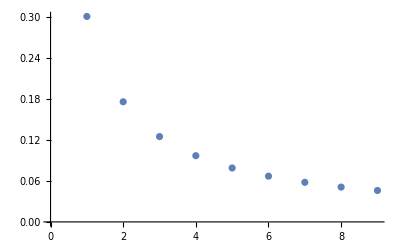

```mathematica
ListPlot@benford
```

Show that the following sets seem to follow Benford’s law: 

1. The first 10000 Fibonacci numbers.
2. The first 10000 Factorials.
3. The first 10000 powers of 2 or Sqrt[2] or 3 (or most functions of the form a^x).

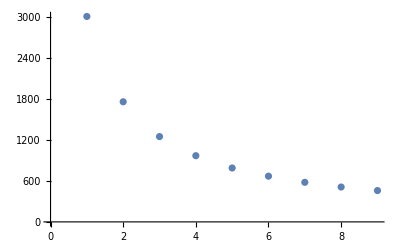

```mathematica
ListPlot@Tally[First/@IntegerDigits[Round[Sqrt[2]^(Range@10000)]]]
```

### Exercise Subsection

Use the code below to show that it is sometimes possible that randomly selected integers from Wikipedia satisfy Benford’s law.

```mathematica
RandomWikipediaNumbers=ToExpression@Table[StringCases[Import["https://en.wikipedia.org/wiki/Special:Random","Plaintext"],DigitCharacter..],10];
First/@IntegerDigits/@RandomChoice/@RandomWikipediaNumbers//Tally//ListPlot
```

## The Fundamental Theorem of Algebra

### Exercise Subsection

The fundamental theorem of algebra says that every nonconstant polynomial f[x] has a complex root; meaning that there is a complex c such that f[c]=0.  Every complex number c can be expressed in polar form as c = r E^(i t) where r is a positive number and t is an angle between 0 and 2 Pi.  Therefore the fundamental theorem of algebra says there is a positive r and a t between 0 and 2 Pi for which both the real and imaginary parts of f[r E^(i t)] is equal to 0. 

Explain how the below cell can be used to illustrate the validity of the fundamental theorem of algebra for the given polynomial f[x].

```mathematica
f[x_]:=x^3+x^2-x+1;
Manipulate[ParametricPlot[{Re[f[r E^(I t)]],Im[f[r E^(I t)]]},{t,0,2Pi},PlotRange->{-5,5},AspectRatio->1],{r,0,3}]
```

## The Shapley value

### Exercise Subsection

A family of 2 parents and 3 children make decisions on what to eat for dinner by voting.  Each parent gets 2 votes, each child 1 vote, and at least 4 votes are needed to win.  What is the Shapley value for each person?

In other words, consider all permutations  of family members.  For each permutation, read from left to right.  The first time that the accumulated coalition gains the power to pick the dinner menu, the person that changed the vote from losing to winning earns one point.  The average point total for each person is the Shapley value.

### Exercise Subsection

Cities within Nassau county (in New York state) were given the number of votes in the next cell, with 16 votes needed to pass a measure.  What is the Shapley value for each city?

```mathematica
Nassau={{"Hempstead1",9},{"Hempstead2",9},{"North Hempstead",7},{"Oyster Bay",3},{"Glen Cove",1},{"Long Beach",1}};
```

## Randomness and Cryptography

### Exercise Subsection

Suppose a company has a file containing the credit card information of its customers secured with a secret integer S. Since the secret S is too important to trust to a single person, the company decides that any subset of size k of a total of n employees should be able to collaborate and determine S while any collection of k−1 employees should not be able to determine S.  The secret sharing scheme is as follows:

1. Let m_0 be a random prime greater than S (say between S and 2*S) and let m_1,..., m_n be the next n primes greater than (2^k)m_0.
2. Select an integer a at random in the range between 0 to Product[m_i,{i,n-k+2,n}]-1.
3. Tell employee i the triple {x_i, m_i, m_0} where x_i is equal to S+a*m_0 modulo m_i.

Then any collection of k employees (employees a through b) can use Mod[ChineseRemainder[{x_a,...,x_b},{m_a,...,m_b}], m_0] to decode the secret S.

Define a function SecretSharing[S_,n_,k_] which has input the secret S, the number of employees n, and the collaboration size k.  The output is a list of triples of the form  {x_i, m_i, m_0} as described above.

### Exercise Subsection

When n=k=2, as secret message text is changed into an integer using  MessageToInteger (as defined in the RSA exercise in Lecture 16) and then the function SecretSharing (as defined in Lecture 16) outputs these triples:

```mathematica
employee1={51370056452106271118179227612094015864084649946225922956070,57899492459644005352797101310930686516110124793260168664731,14474873114911001338199275327732671629027531198315042166151};
employee2={41599382800613239625675899581320616171007158502026240415767,57899492459644005352797101310930686516110124793260168664737,14474873114911001338199275327732671629027531198315042166151};
```

What is the original secret text?

## Benford’s law

### Exercise Subsection

Decide if the following sets satisfy Benford’s law:

1. The first 100000 numbers of the form Binomial[2n,n]/(n+1).
2. The first 100000 integers of the form n^2+n+41.
3. The first 500 numbers found by multiplying together n! and the the coefficient of x^n in the series expansion of Sec[x] + Tan[x] centered at x = 0.
4. The first 100000 prime numbers.
5. The estimated populations of the countries in the following data set:

```mathematica
populations={{"India",1428627663},{"China",1425671352},{"UnitedStates",339996563},{"Indonesia",277534122},{"Pakistan",240485658},{"Nigeria",223804632},{"Brazil",216422446},{"Bangladesh",172954319},{"Russia",144444359},{"Mexico",128455567},{"Ethiopia",126527060},{"Japan",123294513},{"Philippines",117337368},{"Egypt",112716598},{"DRCongo",102262808},{"Vietnam",98858950},{"Iran",89172767},{"Turkey",85816199},{"Germany",83294633},{"Thailand",71801279},{"UnitedKingdom",67736802},{"Tanzania",67438106},{"France",64756584},{"SouthAfrica",60414495},{"Italy",58870762},{"Kenya",55100586},{"Myanmar",54577997},{"Colombia",52085168},{"SouthKorea",51784059},{"Uganda",48582334},{"Sudan",48109006},{"Spain",47519628},{"Argentina",45773884},{"Algeria",45606480},{"Iraq",45504560},{"Afghanistan",42239854},{"Poland",41026067},{"Canada",38781291},{"Morocco",37840044},{"SaudiArabia",36947025},{"Ukraine",36744634},{"Angola",36684202},{"Uzbekistan",35163944},{"Yemen",34449825},{"Peru",34352719},{"Malaysia",34308525},{"Ghana",34121985},{"Mozambique",33897354},{"Nepal",30896590},{"Madagascar",30325732},{"Venezuela",28838499},{"Cameroon",28647293},{"Niger",27202843},{"Australia",26439111},{"NorthKorea",26160821},{"Taiwan",23923276},{"Mali",23293698},{"BurkinaFaso",23251485},{"Syria",23227014},{"SriLanka",21893579},{"Malawi",20931751},{"Zambia",20569737},{"Romania",19892812},{"Chile",19629590},{"Kazakhstan",19606633},{"Chad",18278568},{"Ecuador",18190484},{"Somalia",18143378},{"Guatemala",18092026},{"Senegal",17763163},{"Netherlands",17618299},{"Cambodia",16944826},{"Zimbabwe",16665409},{"Guinea",14190612},{"Rwanda",14094683},{"Benin",13712828},{"Burundi",13238559},{"Tunisia",12458223},{"Bolivia",12388571},{"Haiti",11724763},{"Belgium",11686140},{"Jordan",11337052},{"DominicanRepublic",11332972},{"Cuba",11194449},{"SouthSudan",11088796},{"Sweden",10612086},{"Honduras",10593798},{"Azerbaijan",10412651},{"Greece",10341277},{"PapuaNewGuinea",10329931},{"Portugal",10247605},{"Hungary",10156239},{"Tajikistan",10143543},{"UnitedArabEmirates",9516871},{"Belarus",9498238},{"Israel",9174520},{"Togo",9053799},{"Austria",8958960},{"Switzerland",8796669},{"SierraLeone",8791092},{"Laos",7633779},{"HongKong",7491609},{"Serbia",7149077},{"Nicaragua",7046310},{"Libya",6888388},{"Paraguay",6861524},{"Kyrgyzstan",6735347},{"Bulgaria",6687717},{"Turkmenistan",6516100},{"ElSalvador",6364943},{"Congo",6106869},{"Singapore",6014723},{"Denmark",5910913},{"Slovakia",5795199},{"CentralAfricanRepublic",5742315},{"Finland",5545475},{"Norway",5474360},{"Liberia",5418377},{"StateofPalestine",5371230},{"Lebanon",5353930},{"NewZealand",5228100},{"CostaRica",5212173},{"Ireland",5056935},{"Mauritania",4862989},{"Oman",4644384},{"Panama",4468087},{"Kuwait",4310108},{"Croatia",4008617},{"Eritrea",3748901},{"Georgia",3728282},{"Mongolia",3447157},{"Moldova",3435931},{"Uruguay",3423108},{"PuertoRico",3260314},{"BosniaandHerzegovina",3210847},{"Albania",2832439},{"Jamaica",2825544},{"Armenia",2777970},{"Gambia",2773168},{"Lithuania",2718352},{"Qatar",2716391},{"Botswana",2675352},{"Namibia",2604172},{"Gabon",2436566},{"Lesotho",2330318},{"Slovenia",2119675},{"NorthMacedonia",2085679},{"Latvia",1830211},{"EquatorialGuinea",1714671},{"TrinidadandTobago",1534937},{"Bahrain",1485509},{"Estonia",1322765},{"Mauritius",1300557},{"Cyprus",1260138},{"Eswatini",1210822},{"Djibouti",1136455},{"Réunion",981796},{"Fiji",936375},{"Comoros",852075},{"Guyana",813834},{"Bhutan",787424},{"SolomonIslands",740424},{"Macao",704149},{"Luxembourg",654768},{"Montenegro",626485},{"Suriname",623236},{"CaboVerde",598682},{"WesternSahara",587259},{"Micronesia",544321},{"Malta",535064},{"Maldives",521021},{"Brunei",452524},{"Bahamas",412623},{"Belize",410825},{"Guadeloupe",395839},{"Iceland",375318},{"Martinique",366981},{"Mayotte",335995},{"Vanuatu",334506},{"FrenchGuiana",312155},{"FrenchPolynesia",308872},{"NewCaledonia",292991},{"Barbados",281995},{"Samoa",225681},{"Curaçao",192077},{"SaintLucia",180251},{"Guam",172952},{"Kiribati",133515},{"Grenada",126183},{"Tonga",107773},{"Seychelles",107660},{"Aruba",106277},{"AntiguaandBarbuda",94298},{"IsleofMan",84710},{"Andorra",80088},{"Dominica",73040},{"CaymanIslands",69310},{"Bermuda",64069},{"Greenland",56643},{"FaeroeIslands",53270},{"NorthernMarianaIslands",49796},{"TurksandCaicos",46062},{"SintMaarten",44222},{"AmericanSamoa",43914},{"MarshallIslands",41996},{"Liechtenstein",39584},{"Monaco",36297},{"SanMarino",33642},{"Gibraltar",32688},{"SaintMartin",32077},{"BritishVirginIslands",31538},{"CaribbeanNetherlands",27148},{"Palau",18058},{"CookIslands",17044},{"Anguilla",15899},{"Nauru",12780},{"Tuvalu",11396},{"SaintBarthelemy",10994},{"SaintHelena",5314},{"Montserrat",4386},{"FalklandIslands",3791},{"Niue",1935},{"Tokelau",1893},{"HolySee",518}};
```